# -Graphics-

# Wolfram Language Basics

## Beginning Programming

\[WolframLanguageLogoCircle]

## Outline

### A Basic Introduction to Programming Concepts in the Wolfram Language

Assignments and definitions

Procedural programming

Functional programming

Rule-based programming

## Assignments and Definitions: Overview

Defining and clearing symbols

Immediate and delayed assignments

Making function definitions

## Definitions

The simplest programs are definitions. Definitions are introduced using assignments.

For example, the assignment x=3 assigns 3 as the value of x:

```mathematica
x=3
```

That assignment tells the Wolfram Language™ to replace x by 3 whenever x is encountered during evaluation:

```mathematica
{x,3 x+5}
```

It is good practice to clear assigned values when the definitions are no longer needed, so that assigned values will not interfere with subsequent calculations:

```mathematica
Clear[x]
```

After clearing this definition, x will just evaluate to x:

```mathematica
{x,3 x+5}
```

## Immediate and Delayed Assignments

Assignments can be immediate or delayed.

In an immediate assignment (lhs=rhs), the right side of the assignment is evaluated before the definition is constructed.

In a delayed assignment (lhs:=rhs), the right side of the assignment is not evaluated until the definition is used.

For example, here are two assignments that generate a random number between 0 and 1 using a uniform probability distribution:

```mathematica
rand1=RandomReal[]
```

```mathematica
rand2:=RandomReal[]
```

The only difference between the two assignments is that rand1 uses an immediate assignment and rand2 uses a delayed assignment.

With a delayed assignment, the expansion on the right side of the definition is postponed until the definition is used. But with immediate assignments, the right-hand side of the assignment is evaluated at the time the definition is made, and that value is assigned to the symbol rand1.

This shows the result of repeatedly invoking both functions:

```mathematica
Table[rand1,{3}]
```

```mathematica
Table[rand2,{3}]
```

Clear the definitions before continuing:

```mathematica
Clear[rand1,rand2,f,x]
```

## Using Delayed Assignments

When making an assignment, you need to decide whether the right side of the rule should be evaluated immediately or when the rule is used, and then use the appropriate type of assignment.

Assignments for constants or simple functions are usually done using immediate assignments, as there is no need in such cases to postpone evaluation of the right side of the assignment.

Assignments for nontrivial programs are usually done using delayed assignments, since most programs cannot run as intended until the values of the arguments are known.

For example, the following immediate assignment produces an error message, since the right-hand side cannot be evaluated for unknown n (or, if a rule for n has been previously set up, the wrong definition is made):

```mathematica
g[n_]=Table[i^2,{i,1,n}]
```

This definition is best made with a delayed assignment:

```mathematica
g2[n_]:=Table[i^2,{i,1,n}]
```

```mathematica
g2[5]
```

```mathematica
Clear[g,g2]
```

Tip: Notice the coloring of symbols in the preceding inputs. Put your cursor in one of the cells and select Why the Coloring? from the Help menu to see information about syntax coloring.

Further information: see the Assignments guide page.

## Defining Functions

Delayed assignments are recommended for defining functions.

```mathematica
f[x_]:=x Sin[x]
```

This definition is used when the corresponding function is evaluated:

```mathematica
f[3]
```

The expression f[x_] on the left side of this assignment is a pattern that specifies the class of expressions for which this definition should be used. The pattern f[x_] matches  f[any expression].

The definition  f[x_]:=x Sin[x]: will be applied whenever an expression matching f[x_] is encountered during evaluation.

## Procedural Programming: Overview

Brief discussion of procedures

Predicate functions

Procedural constructs

Localizing variables

## Procedural Programming

Procedural programming means programming using loops, if statements and other functions that control the flow of execution through a program.

For example, a compound expression (a sequence of statements separated by semicolons) is a procedural program.

In a compound expression, the flow of execution is to simply evaluate statements in the order given:

```mathematica
gene=Entity["Gene",{"BRCA1",{"Species"->"HomoSapiens"}}];
chars=Characters[gene["ReferenceSequence"]];
Counts[chars]
```

In most procedural programs, at least part of the flow of execution depends on the values of variables or on the results of various tests. One of the most common procedural constructs is the if control structure. In the Wolfram Language, the If function has the following syntax:

If[test, then, else]

The following example demonstrates how the flow of execution depends on the result of the test x>π:

```mathematica
f[x_]:=If[x>π,
Print[x," is larger than π"],
Print[x," is not larger than π"]
]
```

```mathematica
f[E]
```

## Predicate Functions

Expressions such as Pi>ⅇ that evaluate to True or False are called predicate functions. Many of the predicate functions available in the Wolfram Language are similar to those found in other programming languages.

"Predicate" | "Examples"
"Inequalities" | "x,  x,  x,  x,  x,…"
"Built-in predicates" | "IntegerQ[n], Positive[m], NumberQ[x],…"
"Logical connectives" | "StyleBox[ (logical AND)"

For example, IntegerQ[n]&&n≥0 returns True if n is an integer and n is greater than or equal to zero:

```mathematica
IntegerQ[5]&&5≥0
```

```mathematica
IntegerQ[-7]&&-7≥0
```

Of course, you can define your own predicate functions:

```mathematica
myFilterQ[x_]:=Abs[x]≤1
```

```mathematica
myFilterQ[1.5]
```

Further information: see the tutorial section Putting Constraints on Patterns for an explanation of the  general mechanism for specifying constraints on patterns.

## Procedural Programming Functions

The basic elements of procedural programming are functions used for:

Evaluating a sequence of expressions (called a compound expression):

expr_1;expr_2;expr_3;…

Loops:

Do, For, While, Table, …

Branching (or jumping), depending on a test or condition:

If, Which, Switch

## Example: Summing Integers

Here is a procedural program that computes the sum of the integers 1 through n. The value of n is assigned in the first line of the program.

```mathematica
n=10;
result=0;
Do[result=result+k,{k,1,n}];
result
```

By putting this program on the right side of an assignment, this program can become the definition of a function:

```mathematica
f[n_]:=(
result=0;
Do[result=result+k,{k,1,n}];
result
)
```

You “run” this program by evaluating an expression that matches f[n_]:

```mathematica
f[10]
```

Clear the definition of f before continuing:

```mathematica
Clear[f,n,result]
```

## Example: Checking Arguments

One common use of predicate functions is to check the arguments of functions.

Note that the previous definition of f can give incorrect results if the argument is not a positive integer:

```mathematica
f[n_]:=(
result=0;
Do[result=result+k,{k,1,n}];
result
)
```

Here is a modification of this program, which checks that n is a positive integer before doing the calculation:

```mathematica
f[n_]:=If[IntegerQ[n]&&n>0,
result=0;
Do[result=result+k,{k,1,n}];
result,
Print[n, " is not a positive integer."]
]
```

If the argument is not a positive integer, the print statement in the ELSE clause is evaluated:

```mathematica
f[Pi]
```

```mathematica
f[9]
```

Clear the definition of f before continuing:

```mathematica
Clear[f]
```

## Local Variables

When assignments to temporary variables are used for keeping track of intermediate results, it is common practice, especially in larger programs, to localize those variables to avoid conflicts with other parts of the program.

For example, the assignment to result in the following definition of f could lead to difficulty if f is called from a program that also uses result:

```mathematica
f[n_]:=(
result=0;
Do[result=result+k,{k,1,n}];
result
)
```

Variables can be localized using the Module function. The first argument in Module is a list of variables to localize, and the second argument is the expression to evaluate.

Module[{vars},
 body_of_function
  …]

Here is a definition in which the variable result is localized using Module:

```mathematica
f[n_]:=Module[{result},
result=0;
Do[result=result+k,{k,1,n}];
result
]
```

With this definition, evaluation of f will leave existing values of result unchanged:

```mathematica
result=99
```

```mathematica
f[9]
```

```mathematica
result
```

Variables that have not been localized are called global variables.

The Module function can be used to leave global definitions unchanged.

Clear f and result before continuing:

```mathematica
Clear[f,result]
```

Further information: see the Procedural Programming guide page.

## Functional Programming: Overview

Description of the functional style of programming

Functional constructs such as Map, Apply and Nest

Expressions: atomic and normal (or compound)

Comparison of programming styles

## Functional Programming

Functional programming can be thought of as programming using functions as the arguments of other functions. In this paradigm, computation is viewed as the evaluation of functions.

For example, here is a short procedural program:

```mathematica
gene=Entity["Gene",{"BRCA1",{"Species"->"HomoSapiens"}}];
chars=Characters[gene["ReferenceSequence"]];
Counts[chars]
```

Here is a functional program that does the same calculation:

```mathematica
Counts[Characters[Entity["Gene",{"BRCA1",{"Species"->"HomoSapiens"}}]["ReferenceSequence"]]]
```

## Introducing New Functions

Most nontrivial functional programs require introducing new functions.

For example, consider the task of computing the future value of a principal amount using the formula for compound interest. As a concrete example, consider an interest rate of 5% compounded monthly.

If you start with $1000, this gives the value of your account after one month:

```mathematica
value[p_]:=p(1+(.05)/12)
```

```mathematica
value[1000]
```

Here is the value after two months:

```mathematica
value[value[1000]]
```

And after three months, here is the value of your account:

```mathematica
value[value[value[1000]]]
```

The Nest function is used to iterate functions.

It takes three arguments: the function to iterate, the initial value to pass this function and the number of iterations to perform:

```mathematica
Nest[f,Subscript[x, 0],3]
```

So this computation of future value can be simply done using the function Nest:

```mathematica
Nest[value,1000,3]
```

Here are all the intermediate values for the first 12 months:

```mathematica
NestList[value,1000,12]
```

The basic structure of this example, with a function (like value) that performs a task and another function (like Nest) that invokes the first function, is common to essentially all functional programs. The next few sections explore the most common use of functional constructs using Map and Apply.

## Map

There are many useful functional constructs, like Nest, that are included in the Wolfram Language. One of the most frequently used functions is Map.

Here is an example that illustrates the basic behavior of Map:

```mathematica
Map[f,{4,3,-1,5,-2,1}]
```

Mapping f across more general expressions should help you to see that f is operating on the elements of the expressions on the right:

```mathematica
Map[f,g[a,b,c]]
```

```mathematica
Map[f,a+b+c]
```

Now consider the task of using Map to replace all of the small numbers (defined as close to 0) in a list by their squares.

First define a function that returns the square of a number if the argument is between -1 and 1:

```mathematica
f[x_]:=If[-1<x<1,x^2,x]
```

Map the function f over the elements of a list:

```mathematica
Map[f,{3,.25,-4,-1,-.9,0}]
```

Map hint

This maps the StringLength function over a list of strings:

```mathematica
Map[StringLength,{"How","I","wish","I","could","recollect","pi","easily"}]
```

To clearly describe Map and many similar operations, it is convenient to introduce a bit of terminology.

Clear the definition of f before continuing:

```mathematica
Clear[f]
```

## Atomic Expressions

All visible information in the Wolfram Language is represented using expressions. Expressions are either atomic expressions or normal expressions.

Numbers, symbols and strings are all atomic expressions; they are the basic building blocks of expressions.

"Atom" | "Example"
"Symbol" | "Integrate"
"Integer" | "28"
"Real" | "4.5771"
"Rational" | "2/9"
"Complex" | 3+5 ⅈ
"String" | "The rain in Spain"
"Graph" | -Graphics-
"SparseArray" | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 0 | 0 | 1)

The head of an atomic expression is simply the type of object that it is. The FullForm of an atomic expression is simply that expression:

```mathematica
{Head[17],FullForm[17]}
```

```mathematica
{Head[result],FullForm[result]}
```

```mathematica
{Head["Hello"],FullForm["Hello"]}
```

## Normal Expressions

All other expressions are built up from atomic expressions. These compound expressions are usually called normal expressions and share a common structure: normal expressions have a head and zero or more elements. All normal expressions are of the following form:

h[e_1,e_2,…,e_n]

The h is called the head of the expression and the e_i are the elements. Both the head and the elements of a normal expression can be either atomic expressions or normal expressions themselves.

For example, the expression f[a,b,c] is a normal expression with head f and with three (atomic) elements. The Head function returns the head of its argument:

```mathematica
f[a,b,c]//Head
```

```mathematica
f[a,b,c]//Length
```

Postfix operators

With Part, you can extract any elements:

```mathematica
Part[f[a,b,c],2]
```

It can be a bit more difficult to see the structure of more complicated expressions. For example, here is a nested list of lists, a matrix:

```mathematica
mat={{a,b},{d,e},{g,h}};
```

The FullForm or TreeForm of mat shows its structure:

```mathematica
FullForm[mat]
```

```mathematica
TreeForm[mat]
```

```mathematica
Head[mat]
```

Each of the elements of mat is a list of length 2; there are three of them:

```mathematica
Length[mat]
```

Again, Part is used to extract elements of the expression:

```mathematica
Part[mat,2]
```

Of course, expressions can get quite a bit more complicated to untangle:

```mathematica
TreeForm[poly=x^2+2 x y+y^2-2 x z-2 y z+z^2]
```

Here is the third part of this expression:

```mathematica
poly[[3]]
```

This uniform structure is what makes functional programming so powerful and easy to use.

```mathematica
Clear[mat,poly]
```

## Apply

In addition to Map, another frequently used function is Apply.

Apply[f,expr] replaces the head of expr with f.

Basically, think of using Map when you want to operate on the elements of an expression; use Apply when you want to change the structure of the expression.

This example illustrates the basic behavior of Apply:

```mathematica
Apply[f,g[a,b,c,d,e]]
```

This input uses the Apply function to multiply the elements in a list. Replacing the head of {a,b,c,d,e} with Times gives Times[a,b,c,d,e] as an intermediate result, which then evaluates to the product:

```mathematica
Apply[Times,{a,b,c,d,e}]
```

Using this approach, here is how you might compute 10!:

```mathematica
Apply[Times,{1,2,3,4,5,6,7,8,9,10}]
```

Recalling the example from the previous section on procedural programming, here is a functional approach to adding up the first 10 integers:

```mathematica
Apply[Plus,Range[10]]
```

Alternatively, you could use Total[lis], which adds up the elements of lis:

```mathematica
Total[Range[10]]
```

## Programming Styles

Many simple calculations that might otherwise be done using loops or other procedural programming constructs can be written more succinctly and efficiently as functional programs.

For example, consider the task of finding the largest element in each row of the following matrix:

```mathematica
mat={{3,9,1},{2,7,8},{5,3,1}};
MatrixForm[mat]
```

Here is a procedural program to do this:

```mathematica
result={};
Do[
result=Append[result,Max[mat[[k]]]],
{k,1,3}];
result
```

The notation mat[[k]] in this program corresponds to a function that picks out row k of the matrix:

Here is a functional program that does the same calculation:

```mathematica
Map[Max,mat]
```

Map Hint

To better see what Map is doing here, consider mapping a symbolic function, max, over the matrix.

```mathematica
Clear[max]
```

```mathematica
mat={{3,9,1},{2,7,8},{5,3,1}};
```

```mathematica
Map[max,mat]
```

```mathematica
Clear[mat,result]
```

Further information: see the Functional Programming guide page.

## Programming with Rules: Overview

Replacement rules using ReplaceAll

Pattern matching

Conditional patterns

## Programming with Rules

```mathematica
mat={{0.796495,"N/A",0.070125,-0.323573,0.806554},{"N/A",-0.100365,0.992736,-0.320560,-0.0805351},{0.473571,0.460741,0.030060,-0.412400,0.788522},{0.614974,-0.503201,0.615744,0.966053,-0.011776},{-0.828415,0.035514,0.8911617,"N/A",-0.453926}};
MatrixForm[mat]
```

This replaces all elements in the matrix containing the string "N/A" with 0:

```mathematica
MatrixForm[mat/."N/A"->0]
```

This section shows how to transform any Wolfram Language expression using rules.

## Replacement Rules

Recall that when you make an assignment to a symbol, the value of that symbol is automatically substituted into any expression containing that symbol.

```mathematica
x=5
```

```mathematica
2x+x y
```

This computation can also be done without using definitions. Replacement rules can be used to make substitutions in other expressions without assigning values to symbols.

For example, x → 5 represents a rule for replacing x by 5. The → operator is entered by typing — followed by >.

This input uses the ReplaceAll function and the rule x → 5 to make a substitution for x in the expression 2x+xy:

```mathematica
Clear[x]
```

```mathematica
ReplaceAll[2x+x y,x->5]
```

The basic syntax of ReplaceAll is:

ReplaceAll[expr, pattern -> replacement]

Here is the same input using the shorthand /. operator for ReplaceAll:

```mathematica
2x+x y/.x->5
```

The basic syntax for the shorthand notation is:

expr /. pattern -> replacement

Note that using this replacement rule does not assign any value to x:

```mathematica
?x
```

Replacement rules are often used for replacing elements in an array. This creates a sample 4×4 array of random integers between 0 and 10:

```mathematica
SeedRandom[245];
mat=RandomInteger[{0,10},{4,4}]
```

This replaces all instances of 5 with α and of 3 with β:

```mathematica
mat/.{5->α,3->β}
```

Here is an example of replacement on strings:

```mathematica
StringReplace["the cat in the hat","t"->"T"]
```

In order to gain additional flexibility in transforming expressions, you need to be able to match expressions that satisfy any criteria you might be interested in. The next section looks at patterns, which give that capability.

```mathematica
Clear[mat]
```

## Patterns

The expression on the left side of a rule or assignment is a pattern. This pattern determines the class of expressions to which the corresponding rule applies.

For example, the pattern f[n_] in the following assignment introduces a rule that applies to f[anything]:

```mathematica
f[n_]:=n/(n+1)
```

```mathematica
f[5]
```

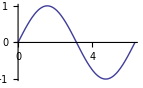
```mathematica
f[-Graphics-]
```

Patterns can be constructed to match any class of expressions. This section uses Cases to return all those elements from a list that match a pattern.

"Pattern" | "Expressions that match" | "Example"
"_" | "any expression" | "x, "a string", 45"
"_Real" | "expression with head Real" | "1.3528"
"_?Negative" | "expression that passes the Negative test" | "-129"
"{p_,q_}" | "list of two expressions" | "{Bob,-0.398}"

```mathematica
?Cases
```

The pattern _ (the underscore character) matches any expression:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_]
```

Named patterns: the pattern x_  gives the matched expression the name x, so that expression can be used elsewhere in the rule.

Matching heads: the pattern _Real matches any number with head Real:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_Real]
```

Matching with predicates: the pattern x_/;Negative[x]matches any negative number.

The following can be read as, "the pattern named x under the condition that x passes the Negative test":

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},n_/;Negative[n]]
```

The shorthand notation  ? exists for a particular conditional pattern.

Here is the test for the same pattern using the shorthand notation:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_?Negative]
```

Matching a pair: the pattern {p_,q_} matches any list containing any two expressions:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},{p_,q_}]
```

```mathematica
Clear[f,g]
```

See the tutorial section Finding Expressions That Match a Pattern for a more complete description of pattern constructions.

## Rules and Pattern Matching

Patterns can be used to prevent rules from being invoked unless certain criteria are met. Patterns are often used in this way to check the validity of arguments.

First, look at an example created earlier:

```mathematica
f[n_]:=If[IntegerQ[n]&&n>0,
result=0;
Do[result=result+k,{k,1,n}];
result,
Print[n, " is not a positive integer."]
]
```

Using patterns, the rule can be set up so that it is used only when the argument is a positive integer:

```mathematica
Clear[f]
```

```mathematica
f[n_Integer?Positive]:=Module[{result=0},
Do[result=result+k,{k,1,n}];
result
]
```

Note also that the local variable result has been initialized inside the Module.

With these definitions, f[Pi] just evaluates to itself, since there are no rules that apply to this expression:

```mathematica
f[Pi]
```

If the argument is a positive integer, the sum is computed as before:

```mathematica
f[100]
```

```mathematica
?f
```

Clear the definition of f:

```mathematica
Clear[f]
```

## Pattern Examples

One way to find out what a pattern matches and to see the pattern in action is to use the pattern in a rule and apply the rule. In this section, you will first use Cases to identify which elements in an expression actually match the given pattern.

In this first example, Cases is used to extract all those elements in the list that match the pattern _Integer (i.e. to return all expressions with head Integer):

```mathematica
Cases[{1,-23,-3.5,4.1,7},_Integer]
```

This replaces the integers in the list by zero:

```mathematica
{1,-23,-3.5,4.1,7}/._Integer->0
```

In this next example, first identify all those elements in the list that pass the Negative test:

```mathematica
Cases[{1,-23,-3.5,4.1,7},_?Negative]
```

This replaces the negative numbers in the list by zero:

```mathematica
{1,-23,-3.5,4.1,7}/._?Negative->0
```

In this example, notice that each of the sublists matches the pattern consisting of a list with two arbitrary elements:

```mathematica
Cases[{{1,2},{3,4},{5,6}},{p_,q_}]
```

This reverses the elements in all lists of two elements:

```mathematica
{{1,2},{3,4},{5,6}}/.{p_,q_}->{q,p}
```

Although this last example seems to work well, what do you think would happen if the expression on the left were a list consisting of exactly two pairs of numbers?

## Conditions on Patterns

You can add conditions to your patterns so that a match only occurs when the condition is satisfied.

This pattern is only matched when the argument to f is less than 0:

```mathematica
f[x_/;x<0]:=x^2
```

```mathematica
f[5]
```

```mathematica
f[-5]
```

Conditions are particularly useful when specifying criteria for functions such as Cases. Here is some synthetic data to work with—a list of 25 random integers between -10 and 10:

```mathematica
data=RandomInteger[{-10,10},25]
```

This returns all those elements in the list data that are between -3 and 3:

```mathematica
Cases[data,p_/;-3≤p≤3]
```

Alternatively, you can delete those elements that match the pattern:

```mathematica
DeleteCases[data,p_/;-3≤p≤3]
```

Other functions use the same syntax as Cases, but return the number of elements that match the pattern or the positions of those elements that match the pattern:

```mathematica
Count[data,p_/;-3≤p≤3]
```

```mathematica
Position[data,p_/;-3≤p≤3]
```

Extract those elements of data that live at these positions:

```mathematica
Extract[data,Position[data,p_/;-3≤p≤3]]
```

```mathematica
Clear[f,data]
```

## Comparing Programming Styles

This section takes a step back and compares the three programming styles—procedural, functional and rule-based—introduced in this chapter through the use of a concrete example.

Nearly all nontrivial programs use a mixture of programming styles. No one style is always better than another. You should choose whatever programming style seems most natural for you or for what you want to do. A good start for learning how to make that decision is to see lots of examples comparing different styles of programming.

As a summary of this introduction to programming in the Wolfram Language, a small problem using three different styles—procedural, functional and rule-based—will be solved: given a list of pairs of numbers, return a list consisting of the sum of each pair.

Here is a list of pairs of numbers:

```mathematica
pairs={{58,96},{85,22},{100,69},{5,37},{32,64},{41,86},{14,0},{79,22},{3,5}};
```

### The Procedural Approach

This is quite similar to what you would do in a language like C or Fortran: allocate an (empty or null) array, result, of the same size as pairs, then replace each element in result by the sum of the first and second elements in each pair. Finally, return the value in result:

```mathematica
result=Table[Null,{Length[pairs]}];
Do[result[[k]]=First[pairs[[k]]]+Last[pairs[[k]]],
{k,1,Length[pairs]}]
result
```

Here is a structured procedure using Table:

```mathematica
Table[pairs[[k,1]]+pairs[[k,2]],{k,Length[pairs]}]
```

### The Functional Approach

This uses Map to apply the Total function to each pair of numbers in the inner lists:

```mathematica
Map[Total,pairs]
```

This gives the column sums of the transpose of the matrix:

```mathematica
Total[Transpose[pairs]]
```

### The Rule-based Approach

This is also quite compact; The pattern to match is any list consisting of a pair of expressions, and it will be replaced by the sum of that pair:

```mathematica
pairs/.{p_,q_}->p+q
```

## Application: Cleaning Up Data

Next, you will combine several of the tools that were introduced in this chapter and apply them to a problem involving raw data. It is not uncommon for data that has been collected in the field or from instruments to contain some non-numeric values.

The array at the beginning of this section is one such example:

```mathematica
mat={{0.796495,"N/A",0.070125,-0.323573,0.806554},{"N/A",-0.100365,0.992736,-0.320560,-0.0805351},{0.473571,0.460741,0.030060,-0.412400,0.788522},{0.614974,-0.503201,0.615744,0.966053,-0.011776},{-0.828415,0.035514,0.8911617,"N/A",-0.453926}};
MatrixForm[mat]
```

Suppose that you needed this matrix to contain all numeric values for subsequent work. With what should you replace the "N/A" entries? In this example, you will replace each "N/A" with the column mean for each such entry; of course, other values could be used.

You will prototype on the first column and then extend that to operate on the entire matrix. Here is the first column of mat:

```mathematica
col1=mat[[All,1]];
MatrixForm[col1]
```

This gives only the numeric values from the first column:

```mathematica
Cases[col1,_?NumberQ]
```

This is the mean of the numeric values:

```mathematica
Mean[Cases[col1,_?NumberQ]]
```

This does the replacement on the first column:

```mathematica
col1/."N/A"->Mean[Cases[col1,_?NumberQ]]//MatrixForm
```

Write a function that performs this operation, but whose argument is the column number. Also, replace col1 with the general term mat[[All,col]]:

```mathematica
fixcolumn[col_]:=mat[[All,col]]/."N/A":>Mean[Cases[mat[[All,col]],_?NumberQ]]
```

Try this function out on column 1 of the matrix:

```mathematica
fixcolumn[1]
```

You need to map this function across all of the columns:

```mathematica
Map[fixcolumn,Range[Length[mat]]]
```

The preceding computation operated on the columns, so the array is a list of the transformed column vectors.

You need to transpose back to put things right:

```mathematica
MatrixForm[Transpose[%]]
```

Next, turn this into a reusable function, FixMatrix:

```mathematica
FixMatrix[mat_]:=Module[{fixcolumn},
fixcolumn[col_]:=mat[[All,col]]/."N/A":>Mean[Cases[mat[[All,col]],_?NumberQ]];
Transpose[Map[fixcolumn,Range[Length[mat]]]]
]
```

```mathematica
FixMatrix[mat]//MatrixForm
```

Now it might be the case that the non-numeric string is something different than "N/A". Here is a second definition for FixMatrix that takes a second argument that is the string to be replaced with its column mean:

```mathematica
FixMatrix[mat_,str_String]:=Module[{fixcolumn},
fixcolumn[col_]:=mat[[All,col]]/.str:>Mean[Cases[mat[[All,col]],_?NumberQ]];
Transpose[Map[fixcolumn,Range[Length[mat]]]]
]
```

```mathematica
mat2={{0.796495,"nan",0.070125,-0.323573,0.806554},{"nan",-0.100365,0.992736,-0.320560,-0.0805351},{0.473571,0.460741,0.030060,-0.412400,0.788522},{0.614974,-0.503201,0.615744,0.966053,-0.011776},{-0.828415,0.035514,0.8911617,"nan",-0.453926}};
MatrixForm[mat2]
```

```mathematica
FixMatrix[mat2,"nan"]//MatrixForm
```

### Going Further

If you want to check a list of different strings, you need to use a slightly different construction.

```mathematica
col={0.796495,"nan",0.070125,-0.323573,"N/A"};
```

```mathematica
col/."N/A"|"nan"->Mean[Cases[mat[[All,1]],_?NumberQ]]//MatrixForm
```

Given a list of strings, you can convert that to a set of alternatives, using Apply:

```mathematica
Apply[Alternatives,{"N/A","nan","nn"}]
```

Finally, here is a third definition that takes a list of strings as the second argument:

```mathematica
FixMatrix[mat_,{strings__}]:=Module[{fixcolumn},
fixcolumn[col_]:=mat[[All,col]]/.Apply[Alternatives,{strings}]->Mean[Cases[mat[[All,col]],_?NumberQ]];
Transpose[Map[fixcolumn,Range[Length[mat]]]]
]
```

```mathematica
mat3={{0.796495,"N/A",0.070125,"N/A",0.806554},
{"nn",-0.100365,0.992736,-0.320560,-0.0805351},
{0.473571,0.460741,0.030060,-0.412400,0.788522},{0.614974,-0.503201,0.615744,0.966053,-0.011776},{-0.828415,0.035514,0.8911617,"nan",-0.453926}};
MatrixForm[mat3]
```

```mathematica
FixMatrix[mat3,{"N/A","nan","nn"}]//MatrixForm
```

## Exercises

### 2.Subsection Creating and Using Definitions

Define a function f[x] that returns x/Sin[x]. Evaluate f[x] for various values of x to verify that your definition is working.

Solution

Plot f[θ]for θ between -10 and 10. Does it make any difference that the variable of the plot is θ and not x?

Solution

Clear your definition of f before continuing.

Solution

### 2.Subsection Making a Table

A common exercise in programming textbooks is constructing a table of integers and squares of integers. There are many ways to do this in the Wolfram Language. One way is to use the Do function, the Print function and a string of spaces to separate the columns in the table.

Evaluate the following input to see the table:

```mathematica
Do[Print[i,"   ",i^2],{i,1,10}]
```

Modify this program to add a column that shows the cube of each integer.

Solution

### 2.Subsection Tables and Grids

One problem with the table in Exercise 2.2 is that the columns are not properly aligned. One solution is to construct the entire table and let the computer align the columns. This can be done in the Wolfram Language using the TableForm function to format the table.

Evaluate the following input to see the table:

```mathematica
mat=Table[{i,i^2},{i,1,10}]
```

This formats the table using a tabular format:

```mathematica
TableForm[mat]
```

You can get more control over the formatting of tabular data using Grid:

```mathematica
Grid[mat,Alignment->Right]
```

Modify this program to add a column that shows the cube of each integer.

Solution

Use replacement rules to modify the last result to add a fourth column that gives the sum of the square and cube in each row.

Solution

### 2.Subsection Matrix Operations

This creates a 6×6 matrix with symbolic elements.

```mathematica
mat=Array[m,{6,6}]
```

You can display the matrix in a traditional form by using MatrixForm.

```mathematica
MatrixForm[mat]
```

Use the Part function to extract the fifth row of mat.

Solution

Use the Part function to extract the third column of mat.

Solution

Use Diagonal to extract the main diagonal from mat.

Solution

Use Diagonal with a second argument to get the diagonal three rows below the main diagonal.

Solution

Use Diagonal (and other functions) to get the diagonal running from the upper right to the lower left.

Solution

### 2.Subsection Picking Out Parts of a Matrix

Evaluate the following input to construct an array of integers and view it as a traditional matrix.

```mathematica
SeedRandom[123];
mat=RandomInteger[{1,9},{6,6}];
MatrixForm[mat]
```

Recall that mat[[k]] picks out a row from a matrix and mat[[All,k]] picks out a column from a matrix. (For more information and additional examples, see the documentation for Part in the Documentation Center.) For example, evaluate the following input to pick out the second column from the matrix mat.

```mathematica
mat[[All,2]]
```

```mathematica
mat[[All,2]]//MatrixForm
```

Often it is useful to pick out several elements from a list or several rows or columns from a matrix. This can be done by listing the positions of the desired elements. For example, evaluate the following input to get a list containing the first and second rows from the matrix mat.

```mathematica
mat[[{1,2}]]
```

Evaluate the following input to get a list containing the first and second columns from the matrix mat.

```mathematica
mat[[All,{1,2}]]//MatrixForm
```

Beginning with the first row, extract every other row in the matrix.

Hint

Consider using the Span function.

Solution

Assign a value of 0 to each of the elements in the last column of matrix mat.

Solution

Assign a value of 0 to each of the elements on the “border” of the matrix, that is, the elements in the first and last rows and the first and last columns.

Solution

### 2.Subsection Immediate and Delayed Assignments

Suppose f[x] is defined as follows:

```mathematica
f[x_]:=3 x^2-2 x
```

Define the derivative of f as a function of x. You can use either immediate assignments (=) or a delayed assignment (:=), but only one of these will work properly with arbitrary arguments. Which type of assignment works correctly and why?

Solution

### 2.Subsection Localizing Variables

Identify the two global variables in this definition. Change this definition so that those two variables are localized using Module:

```mathematica
f[p_,q_]:=(
temp=Solve[p+q x==0,x];
x/.temp
)
```

Hint

The two global variables in this definition are x and temp. The names of named patterns in a rule or definition are automatically localized, so the names p and q in the function arguments are automatically local to this definition of f.

Solution

### 2.Subsection Using Patterns and Rules in Graphics

Evaluate the following input to construct and display a Graphics expression. The argument of the Line primitive in the Graphics expression is a list of pairs of real numbers. Each pair of numbers specifies a coordinate in two dimensions:

```mathematica
gr=Graphics[Line[{{0.0,0.0},{1.0,1.0},{2.0,0.0},{3.0,2.0},{4.0,0.0},{5.0,2.0},{6.0,1.0},{7.0,3.0},{8.0,0.0},{9.0,2.0},{10.0,0.0}}],Axes->True]
```

Apply a rule to this Graphics expression to replace all pairs of real numbers {p_Real,q_Real} with {q,p} so that the coordinates in each pair are reversed. Display the result. This replacement corresponds to exchanging the vertical and horizontal dimensions or, equivalently, to reflecting the image across a diagonal.

Hint

The rule to apply is {p_Real,q_Real}→{q,p}.

Solution

### 2.Subsection Pattern Matching

Define a function abs[x] that returns x whenever x is a positive number, −x whenever x is a negative number, and returns √(a^2+b^2) whenever x is a complex number of the form a+bⅈ (a and b real).

Hint

One approach might use nested If structures. These can often be hard to read and debug, so try instead to create a separate definition for each clause in the statement of the problem.

Consider using the predicate functions NonNegative, Negative, NonPositive, Positive to create the appropriate patterns. You will also need to match the head Complex.

Solution

### 2.Subsection Constructing an Expression

One useful technique for testing and debugging Wolfram Language programs is to observe the results after inserting random numerical values for any symbolic variables in the program.

Using the following list of variables, construct a list of rules for replacing each variable in the list with a value generated using RandomReal:

```mathematica
vars={xxy,xxz,xyy,yxx,yzz,yzy};
```

Hint

Solution

Use your list of rules to find the one symbolic variable in the following expression that is not among the six variables included in the value of vars. After numerical values have been inserted for the listed variables, this expression will collapse to a simple expression in which the extra variable should be obvious:

```mathematica
expr=-(11+11 xxz+7 xyy+21 yzy)/(1+5 xxy+11 xxz+11 yxx)^2+(2 xxy+10 xxz+6 xyy+9 yzy+2 yzz)/(3+11 xxy+5 xxz+14 xyy+5 yzy)^2+(5+10 xxy+7 xxz+11 xyy+8 yxx+4 yzz)^2/(6 xxy+9 xxz+8 xyy+2 yxx+9 yzy)-(4+2 xxy+4 xxz+10 xyy+8 yxx+5 yzy+4 yzz)/(3 xxy+6 xxz+4 yxx+6 yzz)^2+(11 xxy+8 xxz+5 xyy+6 yxy+yzz)/(1+8 xxy+7 xxz+11 yxx+8 yzz)^2+(4 xyy+9 yxx+3 yzy+6 yzz)^2/(3 xxz+19 xyy+15 yzz);
```

Hint

If your solution involves vars and expr, be sure you have evaluated the inputs that define these variables.

Solution

Variation: Suppose you are assigned the task of getting all the symbols used in the expression expr in the preceding expression. Use Cases with level specifications to accomplish the task.

Solution

### 2.Subsection Delayed Rules

Here is a definition for a factorial function using two assignments—one dealing with the base case, or stopping condition, and the other specifying the recursion.

```mathematica
fac[0]=1;
fac[n_]:=n fac[n-1]
```

```mathematica
Table[fac[m],{m,10}]
```

Note that the first definition was given as an immediate assignment and the second definition was given as a delayed assignment.

Create a set of substitution rules and apply them to an expression to compute 10!. You should consider repeated application of your rules (ReplaceRepeated, with shorthand notation //.) as well as delayed rules (RuleDelayed, with shorthand notation :>).

Solution

### 2.Subsection Formatting Numbers in a Table

Evaluate the following two inputs to solve a differential equation and display a table of results. The second column in the table is formatted using PaddedForm, so that each entry in that column has four digits to the right of the decimal point:

```mathematica
Clear[f,t]
```

```mathematica
sol=NDSolve[{f''[t]==2f[t]-25,f[0]==1,f[5]==250},f,{t,0,5}]
```

```mathematica
TableForm[Table[{t,PaddedForm[f[t]/.sol[[1]],{7,4}]},{t,0.0,5,0.5}]]
```

Change the table so that the entries in the first column are formatted with one digit to the right of the decimal point. The resulting table should look like this:

0.0 |    1.0000
 0.5 |    7.1394
 1.0 |   10.4849
 1.5 |   12.7801
 2.0 |   15.2213
 2.5 |   19.0808
 3.0 |   26.3701
 3.5 |   40.8882
 4.0 |   70.2018
 4.5 |  129.5886
 5.0 |  250.0000

Hint

You can use PaddedForm[t,{2,1}] to display the number t so that the display shows one digit to the right of the decimal point.

Solution

### 2.Subsection Programming Style

Evaluate the following input to define data to be a list of pairs of elements:

```mathematica
data={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
```

Here is a procedural program that reverses the elements in each pair. Evaluate this input to get the result. This program works by initializing a list in which all the elements are Null and then assigning each element in that list to be the reverse of the corresponding element from data:

```mathematica
result=Table[Null,{Length[data]}];
Do[
result[[k]]=Reverse[data[[k]]],
{k,1,Length[data]}
];
result
```

Here is a functional program that gives the same result:

```mathematica
Map[Reverse,data]
```

Here is a program that uses a rule to get the same result:

```mathematica
data/.{p_,q_}->{q,p}
```

Modify these programs so that the result is a list of the first element in each pair. For data, the result from each program will be {x1,x2,x3,x4,x5}.

Hint

The function First can be used to pick out the first element in a list.

The procedural program and the functional program can be modified to give the desired result by simply replacing Reverse with First.

The rule {p_,q_]→p will replace a pair of elements with the first element from that pair.

Solution

Now modify these programs so that each program returns a list containing the sum of the elements in each pair.

Hint

Here are two procedural programs that return a list giving the sum of the elements in each pair.

```mathematica
result=Table[Null,{Length[data]}];
Do[
result[[k]]=data[[k,1]]+data[[k,2]],
{k,1,Length[data]}
];
result
```

```mathematica
Table[data[[k,1]]+data[[k,2]],{k,Length[data]}]
```

Solution

### 2.Subsection Debugging a Procedural Program

Evaluate the following input to define a function f that takes a matrix as an argument. This function is intended to return the row from that matrix for which the first element has the largest absolute value:

```mathematica
f[m_]:=Module[{result},
{result=m[[1]];
Do[
If[Abs[m[[k,1]]]>Abs[result[[1]]],
result=m[[k]]],
{k,2,Length[m]}
]
result}
]
```

Evaluate the following input and note that this program does not do what it is intended to do. It returns the correct row from the matrix, but each element in that row is multiplied by Null, and that row is enclosed in an unwanted list:

```mathematica
f[({{1, 4, 7}, {9, 1, 8}, {4, 6, 1}, {11, 5, 8}, {6, 1, 1}})]
```

Correct the two errors in this program so that the result for the example is {11,5,8}.

Hint

The body of the Module (the second argument in the Module expression) should not be enclosed in curly braces.

Unnecessary curly braces are often included in this type of program by people who have experience programming in C.

The return value of Do is Null. As defined, the return value of this program is the return value of the Do loop multiplied by result.

Solution